```mathematica
SetDirectory[NotebookDirectory[]];
```

### Figure 3.2

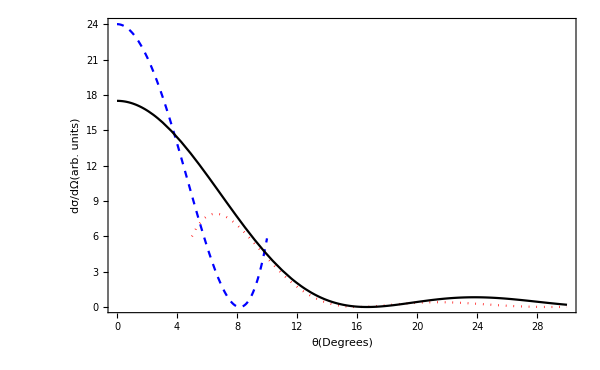

fig3_2.png

```mathematica
R=7;
k=2;
scale=1/100;
dσ1=scale*(2R)/(π*k*(θ*Degree)^2*Sin[θ*Degree])Cos[k*R*θ*Degree+π/4]^2;
dσ2=scale*(k^2 R^4)/4(1-(k*R*θ*Degree/2)^2)^2;
dσ3=scale*1750*Sinc[k*5.4*θ*Degree]^2;
p1=Plot[dσ1,{θ,5,30},PlotRange->All,PlotStyle->{Red,Dotted}];
p2=Plot[dσ2,{θ,0,10},PlotRange->All,PlotStyle->{Blue,Dashed}];
p3=Plot[dσ3,{θ,0,30},PlotRange->All,PlotStyle->Black];
final=Show[p1,p2,p3,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"θ(Degrees)","dσ/dΩ(arb. units)"},LabelStyle->{15,Black},ImageSize->600]
Export["fig3_2.png",final]
```

```mathematica
Directory[]
```

/home/clpetrie